```mathematica
α2=0.47104500698378393;
σ2=0.21706585496978287;
```

```mathematica
mD2=0.18764366844838265;
```

```mathematica
T2=0.1642;
```

```mathematica
ϵp[p_,mD_,T_]:=p^2/(p^2+mD^2)-ⅈ π T(p^2 mD^2)/(p(p^2+mD^2)^2);
```

```mathematica
ϵo[r_,mD_,T_]:=-(ⅇ^(-mD r) mD^2)/(4π r)-ⅈ T(mD √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4])/(4 π r);
```

```mathematica
Imϵr[r_,mD_,T_,reg_]:=-(4 π^2 mD T)/(2π)^2 Quiet[NIntegrate[p^2(p^2 mD^2)/((p^2+reg^2)^(1/2)(p^2+mD^2)^2)Sinc[p r],{p,0,∞},MaxRecursion->20]];
```

```mathematica
Imϵr1[r_,mD_,T_,reg_]:=-(4 π^2 mD T)/(2π)^2 NIntegrate[p^2(p^2 mD^2)/((p+reg)(p^2+mD^2)^2)Sinc[p r],{p,0,∞}];
```

```mathematica
ImϵrintermD=Quiet[Interpolation[ParallelTable[{r,Imϵr[r,mD2,T2,mD2]},{r,1/100,200,1/100}]]];
```

```mathematica
Imϵrinterl=Quiet[Interpolation[ParallelTable[{r,Imϵr[r,mD2,T2,0.005]},{r,1/100,200,1/100}]]];
```

```mathematica
Imϵrinterh=Quiet[Interpolation[ParallelTable[{r,Imϵr[r,mD2,T2,1]},{r,1/100,200,1/100}]]];
```

```mathematica
Imϵrinterl
```

InterpolatingFunction[{{0.01, 200.}}, <>]

```mathematica
Plot[Imϵrinter[x],{x,1/100,52}]
```

-Graphics-

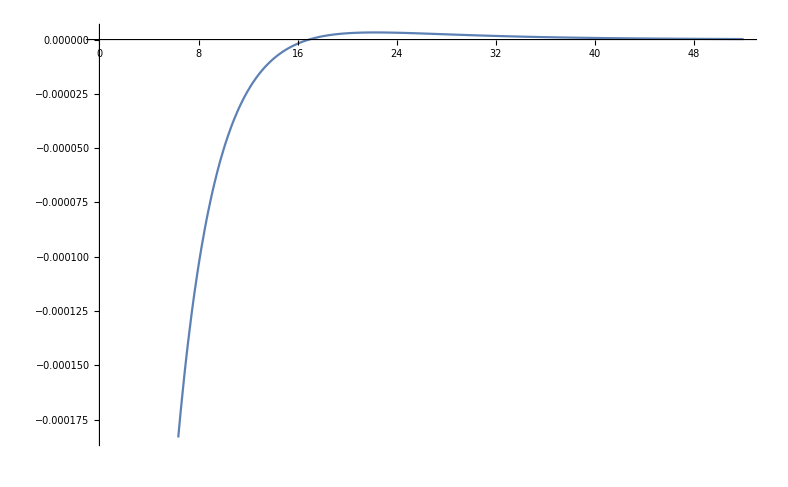

```mathematica
Plot[Im[ϵo[x,2/10,155/1000]],{x,1/100,52}]
```

```mathematica
Clear[tab0,inter0,inter1,temp,tab1,inter1,inter2,tab2,res,resh]
```

```mathematica
tab0=Quiet[ParallelTable[{r,-4π σ2 r^2 Imϵrinterl[r]},{r,1/100,50,1/100}]];
inter0=Quiet[Interpolation[tab0]];
inter1[r_]:=Quiet[NIntegrate[inter0[r1],{r1,0,r}]];
temp=inter1[0];
tab1=Quiet[ParallelTable[{r,inter1[r]-temp},{r,1/100,50,1/100}]];
inter1=Quiet[Interpolation[tab1]];
inter2[r_]:=Quiet[NIntegrate[inter1[r1],{r1,0,r}]];
tab2=Quiet[ParallelTable[{r,inter2[r]},{r,0,50,1/100}]];
resl=Quiet[Interpolation[tab2]]
```

InterpolatingFunction[{{0., 50.}}, <>]

```mathematica
Clear[tab0,inter0,inter1,temp,tab1,inter1,inter2,tab2,res,resh]
```

```mathematica
tab0=Quiet[ParallelTable[{r,-4π σ2 r^2 ImϵrintermD[r]},{r,1/100,50,1/100}]];
inter0=Quiet[Interpolation[tab0]];
inter1[r_]:=Quiet[NIntegrate[inter0[r1],{r1,0,r}]];
temp=inter1[0];
tab1=Quiet[ParallelTable[{r,inter1[r]-temp},{r,1/100,50,1/100}]];
inter1=Quiet[Interpolation[tab1]];
inter2[r_]:=Quiet[NIntegrate[inter1[r1],{r1,0,r}]];
tab2=Quiet[ParallelTable[{r,inter2[r]},{r,0,50,1/100}]];
res=Quiet[Interpolation[tab2]]
```

InterpolatingFunction[{{0., 50.}}, <>]

```mathematica
Clear[tab0,inter0,inter1,temp,tab1,inter1,inter2,tab2,resh]
```

```mathematica
tab0=Quiet[ParallelTable[{r,-4π σ2 r^2 Imϵrinterh[r]},{r,1/100,50,1/100}]];
inter0=Quiet[Interpolation[tab0]];
inter1[r_]:=Quiet[NIntegrate[inter0[r1],{r1,0,r}]];
temp=inter1[0];
tab1=Quiet[ParallelTable[{r,inter1[r]-temp},{r,1/100,50,1/100}]];
inter1=Quiet[Interpolation[tab1]];
inter2[r_]:=Quiet[NIntegrate[inter1[r1],{r1,0,r}]];
tab2=Quiet[ParallelTable[{r,inter2[r]},{r,0,50,1/100}]];
resh=Quiet[Interpolation[tab2]]
```

InterpolatingFunction[{{0., 50.}}, <>]

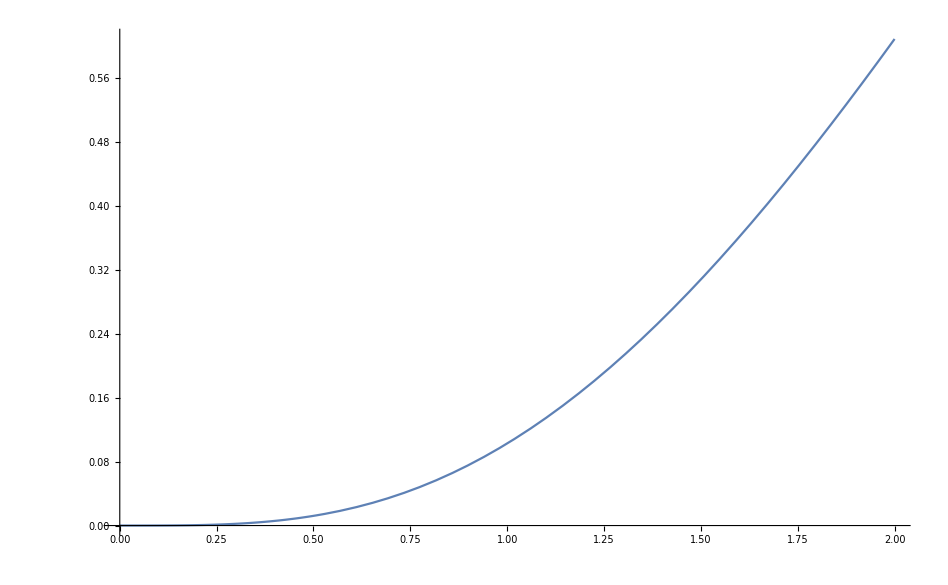

```mathematica
Plot[res[x/0.197],{x,0,2}]
```

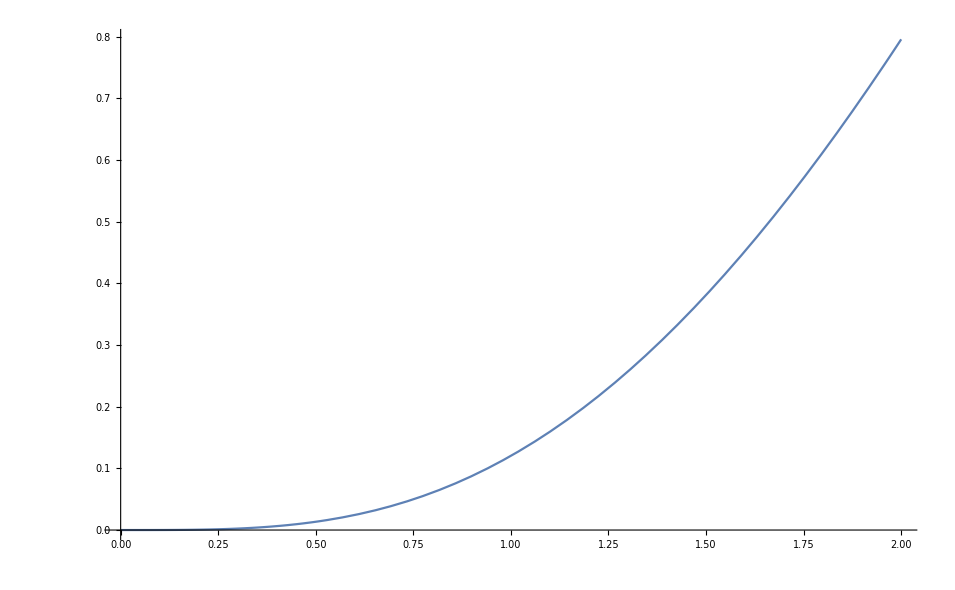

```mathematica
Plot[resl[x/0.197],{x,0,2}]
```

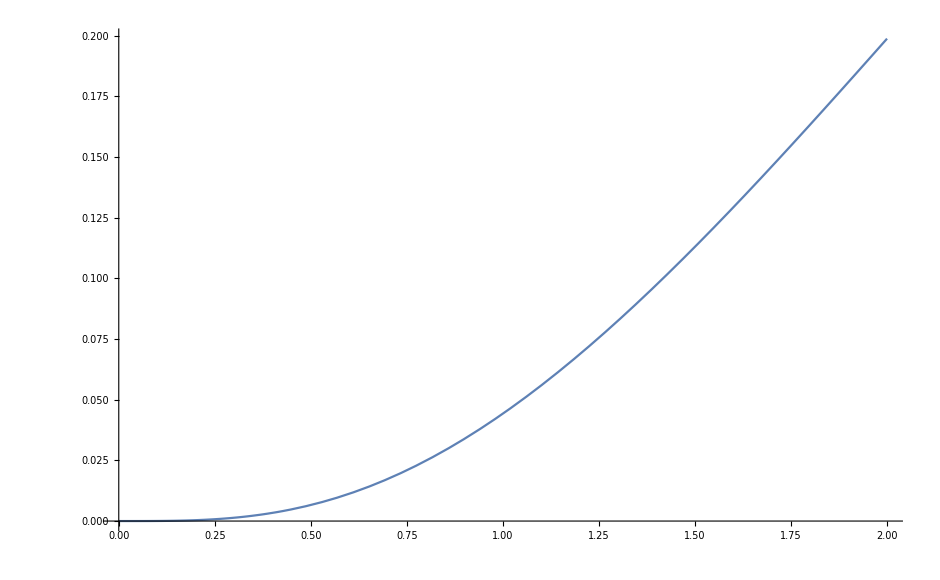

```mathematica
Plot[resh[x/0.197],{x,0,2}]
```

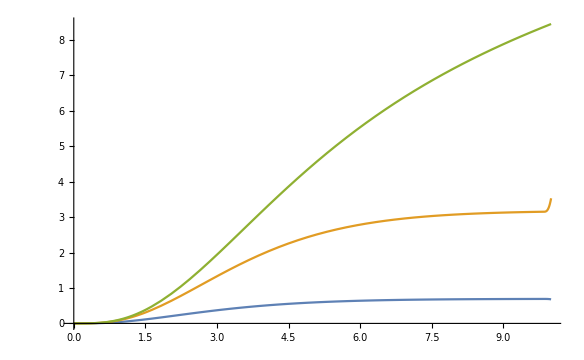

```mathematica
Plot[{resh[x/0.197],res[x/0.197],resl[x/0.197]},{x,0,10}]
```

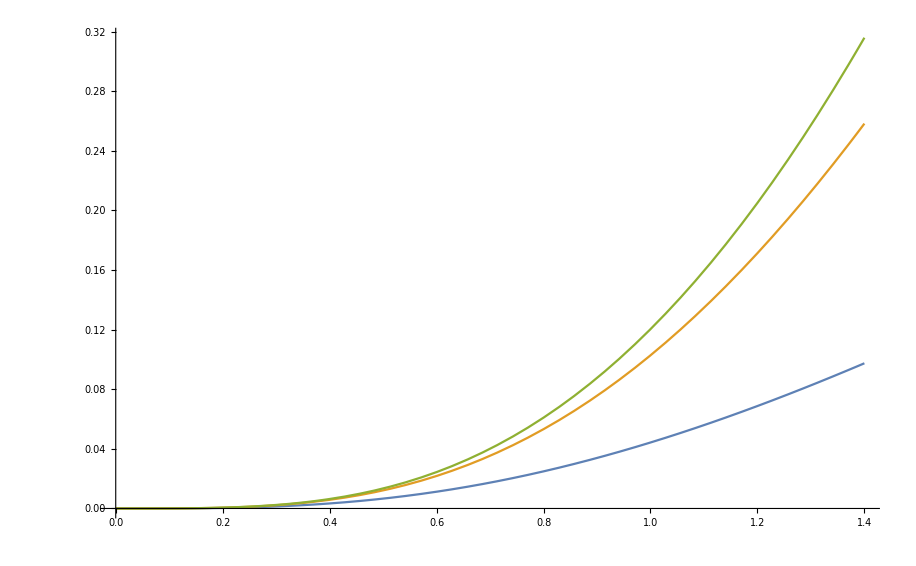

```mathematica
Plot[{resh[x/0.197],res[x/0.197],resl[x/0.197]},{x,0,1.4}]
```